```mathematica
f[x_]:=Piecewise[{{x-1,x≤1},{x^2-1,x<3},{Sqrt[x-3],x≥3}}]
PlotPiecewise[f[x],{x,-2,5},PlotTheme->"Monochrome",GridLines->Automatic]
```

-Graphics-

```mathematica
ClearAll[f,x]
```

```mathematica
f[x_]:=(x^2+x-6)/(x^2-5x+6)
Limit[f[x],x->2]
```

-5

```mathematica
(x-2)(x-3)//Expand//TraditionalForm
```

x^2-5 x+6

```mathematica
Factor[x^4-16]
```

```mathematica
(x-2)(x-1)//Expand
x^4-16//Factor
```

2-3 x+x^2

(-2+x) (2+x) (4+x^2)

```mathematica
Solve[4==(y+2)/(x-1),y]
```

{{y→2 (-3+2 x)}}

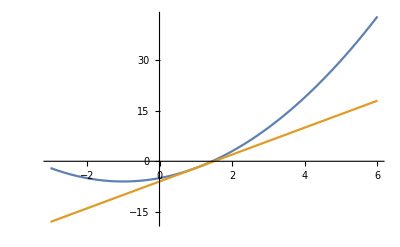

```mathematica
Plot[{x^2+2x-5,4x-6},{x,-3,6}]
```